```mathematica
SetDirectory[NotebookDirectory[]];
Get[FileNameJoin[{Directory[],"HexaBoxModules.m"}]];
PureIntegrals=ReadList[FileNameJoin[{NotebookDirectory[],"files/PureIntegralBasisFull.txt"}]];
PureIntegralsNEW=ReadList[FileNameJoin[{NotebookDirectory[],"files/PureIntegralBasis1-111.txt"}]];
$P=2^31-1;
CayleyEntry[i_,j_]:=Module[{mat},
If[i==0 && j==0 ,
Return[0];
];
If[i==0 || j==0 ,
Return[1];
];

If[i==j,
mat=2msq[i]/.intMasses;
Return[mat];
];
If[i<j,
mat=((msq[i]/.intMasses)+(msq[j]/.intMasses)-Expand[(Sum[q[n],{n,i,j-1}])^2])/.mandelstamScalarProducts/.kinematics;
Return[mat];
];
If[i>j,
mat=CayleyEntry[j,i];
Return[mat];
];
]
cutCayley[mat_,l_]:=Module[{res},
res=mat;
res=Delete[res,l];
res=Transpose[Delete[Transpose[res],l]];
res
]



RemainingInts=PureIntegrals[[103;;]];
InvariantsConvChange={p1s->s56,s12->s123,s23->s34,s34->s23,s45->s12,s15->s234};
(sqrtG3Exp = Sqrt[p1s^2 + (s23 - s45)^2 - 2*p1s*(s23 + s45)]/.InvariantsConvChange)/.Sqrt[x_]:>x//Expand
invariantConvChange={s23->s345,s45->s12,s15->s16,mTsq->mt2};
sqrtG3DB=Sqrt[(-mTsq+s23-s45)^2-4 mTsq s45]/.invariantConvChange/.Sqrt[x_]:>x//Expand
```

s12^2-2 s12 s34+s34^2-2 s12 s56-2 s34 s56+s56^2

mt2^2-2 mt2 s12+s12^2-2 mt2 s345-2 s12 s345+s345^2

```mathematica
Position[(RemainingInts/.hxb:>List)[[All,4]],0]
```

{{53},{54},{55},{56},{57},{58},{59},{60},{61}}

```mathematica
RemainingInts[[53;;61]]
```

{hxb[1,0,1,0,0,0,1,1,1,0,0,0,0],hxb[1,0,1,0,0,1,0,1,0,0,0,0,0],hxb[1,0,1,0,0,1,0,1,1,0,0,0,0],hxb[1,0,1,0,0,1,1,1,1,0,0,0,0],hxb[1,0,1,0,1,0,1,1,0,0,0,0,0],hxb[1,0,1,0,1,0,1,1,1,0,0,0,0],hxb[1,0,1,0,1,1,0,1,1,0,0,0,0],hxb[1,0,1,0,1,1,1,1,0,0,0,0,0],hxb[1,0,1,0,1,1,1,1,1,0,0,0,0]}

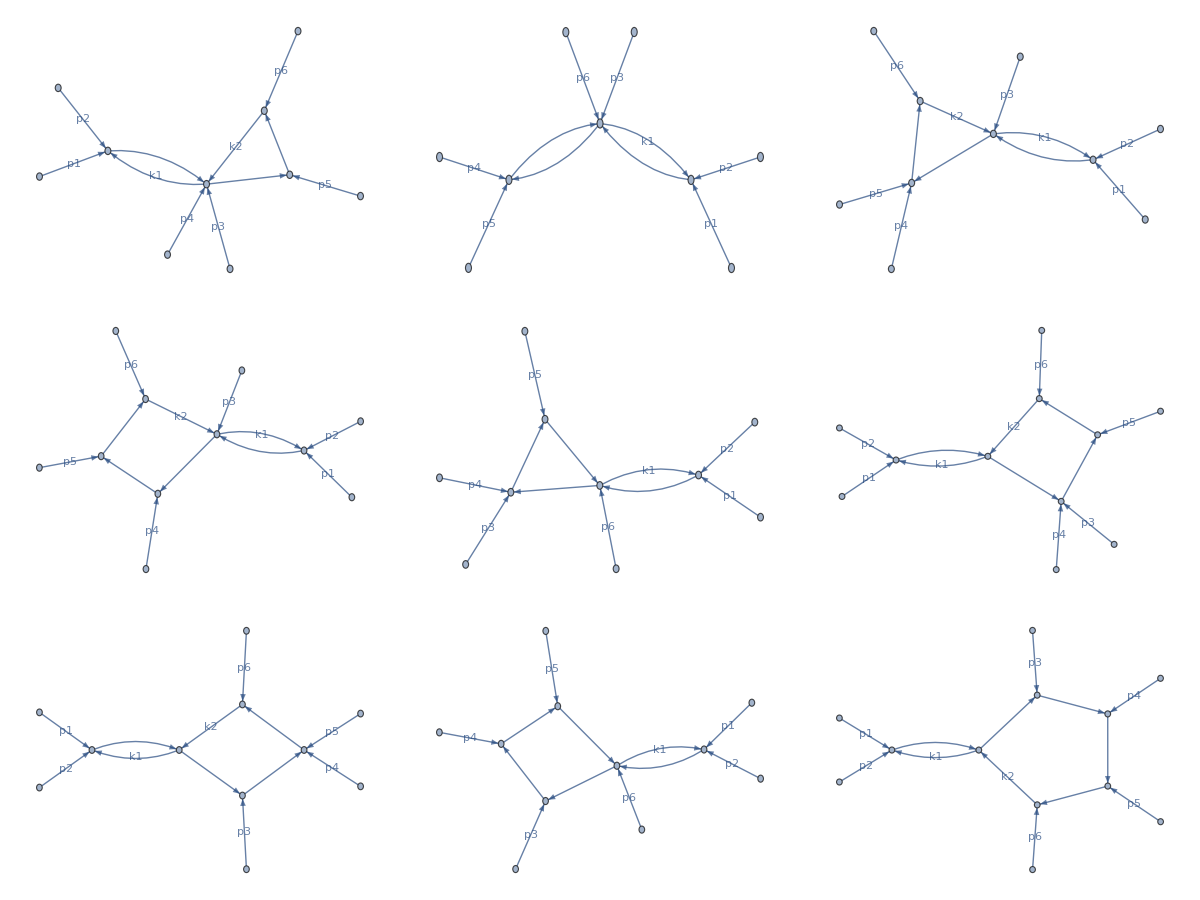

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
For[i=53,i<=61,i++,
FactorPlot[i]=plotDiagram[RemainingInts[[i]]];
]
Print[Grid[ArrayReshape[{Table[FactorPlot[i],{i,53,61}]},{3,3}]]];
```

# Diagram 1

```mathematica
q[1]=p[1]+p[2]+p[3]+p[4];
q[2]=p[5];
intMasses={msq[1]->0,msq[2]->0,msq[3]->mt2};
modcayleyMat=Table[CayleyEntry[i,j],{i,0,3},{j,0,3}];
modcayleyMat//MatrixForm
kP=3+1;
LS=2^(-kP/2+1)/root[(-1)^Floor[kP/2] Det[modcayleyMat]]
BasisChange[1]=ϵ^3/LS*2(-3+d)
```

(0 | 1 | 1 | 1
1 | 0 | -s56 | 0
1 | -s56 | 0 | 0
1 | 0 | 0 | 2 mt2)

1/(2 root[-4 mt2 s56+s56^2])

4 (-3+d) ϵ^3 root[-4 mt2 s56+s56^2]

4 (-3+d) ep^3 hxb[1,0,1,0,0,0,1,1,1,0,0,0,0] root[-4 mt2 s56+s56^2]

# Diagram 2

```mathematica
q[1]=p[4]+p[5];
q[2]=-q[1];
intMasses={msq[1]->0,msq[2]->mt2};
modcayleyMat=Table[CayleyEntry[i,j],{i,1,2},{j,1,2}];
modcayleyMat//MatrixForm
kP=2;
LS=2^(-kP/2+1)/root[(-1)^Floor[kP/2] Det[modcayleyMat]]/.root[x_]:>root[Factor[x]]/.root[x_^2]:>x 
Extras=(-(-2+d)(mt2+s45))/(2mt2(mt2-s45)^2)*PR[6]+(2(-3+d)s45)/(mt2-s45)^2;
BasisChange[2]=ϵ^2/LS*2(-3+d)*Extras
PureIntegrals[[156]]
(*plotDiagram[PureIntegrals[[156]]]*)
Collect[Expand[BasisChange[2]*PureIntegrals[[156]]],hxb[___],Factor]
```

(0 | mt2-s45
mt2-s45 | 2 mt2)

1/(mt2-s45)

2 (-3+d) (mt2-s45) ϵ^2 ((2 (-3+d) s45)/(mt2-s45)^2+((2-d) (mt2+s45) PR[6])/(2 mt2 (mt2-s45)^2))

hxb[1,0,1,0,0,1,0,1,0,0,0,0,0]

-((-3+d) (-2+d) (mt2+s45) ϵ^2 hxb[1,0,1,0,0,0,0,1,0,0,0,0,0])/(mt2 (mt2-s45))+(4 (-3+d)^2 s45 ϵ^2 hxb[1,0,1,0,0,1,0,1,0,0,0,0,0])/(mt2-s45)

# Diagram 3

```mathematica
q[1]=p[4]+p[5];
q[2]=p[1]+p[2]+p[3];
q[3]=-q[1]-q[2];
intMasses={msq[1]->mt2,msq[2]->0,msq[3]->0};
modcayleyMat=Table[CayleyEntry[i,j],{i,0,3},{j,0,3}];
modcayleyMat//MatrixForm
kP=3+1;
LS=2^(-kP/2+1)/root[(-1)^Floor[kP/2] Det[modcayleyMat]]
BasisChange[3]=ϵ^3/LS*2(-3+d)
```

(0 | 1 | 1 | 1
1 | 2 mt2 | mt2-s45 | 0
1 | mt2-s45 | 0 | -s123
1 | 0 | -s123 | 0)

1/(2 root[mt2^2-2 mt2 s123+s123^2-2 mt2 s45-2 s123 s45+s45^2])

4 (-3+d) ϵ^3 root[mt2^2-2 mt2 s123+s123^2-2 mt2 s45-2 s123 s45+s45^2]

# Diagram 4

```mathematica
q[1]=p[5];
q[2]=p[4];
q[3]=p[1]+p[2]+p[3];
q[4]=-q[1]-q[2]-q[3];
intMasses={msq[1]->mt2,msq[2]->0,msq[3]->0,msq[4]->0};
modcayleyMat=Table[CayleyEntry[i,j],{i,1,4},{j,1,4}];
modcayleyMat//MatrixForm
kP=4;
LS=2^(-kP/2+1)/root[(-1)^Floor[kP/2] Det[modcayleyMat]]/.root[x_]:>root[Factor[x]]/.root[x_^2 y_^2]:>x y
BasisChange[4]=ϵ^3/LS*2(-3+d)
```

(2 mt2 | 0 | mt2-s45 | 0
0 | 0 | 0 | -s56
mt2-s45 | 0 | 0 | -s123
0 | -s56 | -s123 | 0)

1/(2 (mt2-s45) s56)

4 (-3+d) (mt2-s45) s56 ϵ^3

# Diagram 5

```mathematica
q[1]=p[3]+p[4];
q[2]=p[6]+p[1]+p[2]/.p4cons;
q[3]=-q[1]-q[2];
intMasses={msq[1]->0,msq[2]->0,msq[3]->mt2};
modcayleyMat=Table[CayleyEntry[i,j],{i,0,3},{j,0,3}];
modcayleyMat//MatrixForm
kP=3+1;
LS=2^(-kP/2+1)/root[(-1)^Floor[kP/2] Det[modcayleyMat]]
BasisChange[5]=ϵ^3/LS*2(-3+d)
```

(0 | 1 | 1 | 1
1 | 0 | -s34 | 0
1 | -s34 | 0 | mt2-s345
1 | 0 | mt2-s345 | 2 mt2)

1/(2 root[mt2^2-2 mt2 s34+s34^2-2 mt2 s345-2 s34 s345+s345^2])

4 (-3+d) ϵ^3 root[mt2^2-2 mt2 s34+s34^2-2 mt2 s345-2 s34 s345+s345^2]

# Diagram 6

```mathematica
q[1]=p[1]+p[2];
q[2]=p[3]+p[4];
q[3]=p[5];
q[4]=-q[1]-q[2]-q[3];
intMasses={msq[1]->0,msq[2]->0,msq[3]->0,msq[4]->mt2};
modcayleyMat=Table[CayleyEntry[i,j],{i,1,4},{j,1,4}];
modcayleyMat//MatrixForm
kP=4;
LS=2^(-kP/2+1)/root[(-1)^Floor[kP/2] Det[modcayleyMat]]
BasisChange[6]=ϵ^3/LS*2(-3+d)
```

(0 | -s12 | -s56 | 0
-s12 | 0 | -s34 | mt2-s345
-s56 | -s34 | 0 | 0
0 | mt2-s345 | 0 | 2 mt2)

1/(2 root[-4 mt2 s12 s34 s56+mt2^2 s56^2-2 mt2 s345 s56^2+s345^2 s56^2])

4 (-3+d) ϵ^3 root[-4 mt2 s12 s34 s56+mt2^2 s56^2-2 mt2 s345 s56^2+s345^2 s56^2]

```mathematica
(*vectors={p[1]+p[2],p[3]+p[4],p[5]}
GramMat=Det[Expand[Table[vectors[[i]]vectors[[j]],{i,1,3},{j,1,3}]]/.kinematics/.mandelstamScalarProducts]*)
```

# Diagram 7

```mathematica
q[1]=p[1]+p[2];
q[2]=p[3];
q[3]=p[5]+p[4];
q[4]=-q[1]-q[2]-q[3];
intMasses={msq[1]->0,msq[2]->0,msq[3]->0,msq[4]->mt2};
modcayleyMat=Table[CayleyEntry[i,j],{i,1,4},{j,1,4}];
modcayleyMat//MatrixForm
kP=4;
LS=2^(-kP/2+1)/root[(-1)^Floor[kP/2] Det[modcayleyMat]]/.root[x_]:>root[Factor[x]]/.root[x_^2]:>x 
BasisChange[7]=ϵ^3/LS*2(-3+d)
```

(0 | -s12 | -s123 | 0
-s12 | 0 | 0 | mt2-s345
-s123 | 0 | 0 | mt2-s45
0 | mt2-s345 | mt2-s45 | 2 mt2)

1/(2 (mt2 s12-mt2 s123+s123 s345-s12 s45))

4 (-3+d) (mt2 s12-mt2 s123+s123 s345-s12 s45) ϵ^3

# Diagram 8

```mathematica
q[1]=p[4];
q[2]=p[3];
q[3]=(p[1]+p[2]+p[6])/.p4cons;
q[4]=-q[1]-q[2]-q[3];
intMasses={msq[1]->0,msq[2]->0,msq[3]->0,msq[4]->mt2};
modcayleyMat=Table[CayleyEntry[i,j],{i,1,4},{j,1,4}];
modcayleyMat//MatrixForm
kP=4;
LS=2^(-kP/2+1)/root[(-1)^Floor[kP/2] Det[modcayleyMat]]/.root[x_]:>root[Factor[x]]/.root[x_^2 y_^2]:>x y 
BasisChange[8]=ϵ^3/LS*2(-3+d)
```

(0 | 0 | -s34 | 0
0 | 0 | 0 | mt2-s45
-s34 | 0 | 0 | mt2-s345
0 | mt2-s45 | mt2-s345 | 2 mt2)

1/(2 s34 (mt2-s45))

4 (-3+d) s34 (mt2-s45) ϵ^3

# Diagram 9

```mathematica
q[1]=p[1]+p[2];
q[2]=p[3];
q[3]=p[4];
q[4]=p[5];
q[4]=-q[1]-q[2]-q[3]-q[4];
intMasses={msq[1]->0,msq[2]->0,msq[3]->0,msq[4]->0,msq[5]->mt2};
modcayleyMat=Table[CayleyEntry[i,j],{i,0,5},{j,0,5}];
modcayleyMat//MatrixForm
kP=5+1;
LS=2^(-kP/2+1)/root[(-1)^Floor[kP/2] Det[modcayleyMat]]/.root[x_]:>root[Factor[x]]/.root[x_^2 y_^2]:>x y
```

(0 | 1 | 1 | 1 | 1 | 1
1 | 0 | -s12 | -s123 | -s56 | 0
1 | -s12 | 0 | 0 | -s34 | -mt2-s12-s34+s345+s56
1 | -s123 | 0 | 0 | 0 | -mt2-s123+s45+s56
1 | -s56 | -s34 | 0 | 0 | 0
1 | 0 | -mt2-s12-s34+s345+s56 | -mt2-s123+s45+s56 | 0 | 2 mt2)

1/(4 root[mt2^2 s12^2-2 mt2^2 s12 s123+mt2^2 s123^2-2 mt2^2 s12 s34+2 mt2^2 s123 s34+2 mt2 s12 s123 s34-2 mt2 s123^2 s34+mt2^2 s34^2-2 mt2 s123 s34^2+s123^2 s34^2+2 mt2 s12 s123 s345-2 mt2 s123^2 s345-2 mt2 s123 s34 s345-2 s123^2 s34 s345+s123^2 s345^2-2 mt2 s12^2 s45+2 mt2 s12 s123 s45+4 mt2 s12 s34 s45-2 mt2 s123 s34 s45+2 s12 s123 s34 s45-2 mt2 s34^2 s45-2 s123 s34^2 s45-2 s12 s123 s345 s45+2 s123 s34 s345 s45+s12^2 s45^2-2 s12 s34 s45^2+s34^2 s45^2-2 mt2 s12 s345 s56+2 mt2 s123 s345 s56-2 mt2 s34 s345 s56+2 s123 s34 s345 s56-2 s123 s345^2 s56+2 mt2 s12 s45 s56-2 mt2 s123 s45 s56+2 mt2 s34 s45 s56-4 s12 s34 s45 s56+2 s123 s34 s45 s56+2 s12 s345 s45 s56+2 s123 s345 s45 s56+2 s34 s345 s45 s56-2 s12 s45^2 s56-2 s34 s45^2 s56+s345^2 s56^2-2 s345 s45 s56^2+s45^2 s56^2])

```mathematica
vectors={p[1]+p[2],p[3],p[4],p[5]};
Gram1=Det[Expand[Table[vectors[[i]]vectors[[j]],{i,1,4},{j,1,4}]]/.kinematics/.mandelstamScalarProducts];
vectors2={p[1]+p[2],p[3],p[4],p[5],k[2]};
Baikov=Factor[Expand[Det[Expand[Table[vectors2[[i]]vectors2[[j]],{i,1,5},{j,1,5}]]/.loopMomentumScalarProducts/.kinematics/.mandelstamScalarProducts]]];
```

```mathematica
BasisChange[9]=ϵ^4/LS*2(-3+d)*(2*Baikov)/(Gram1*(d-4));
```

```mathematica
For[i=1,i<=9,i++,
NewBasis[i]=Collect[Expand[BasisChange[i]RemainingInts[[52+i]]],{hxb[___],root[___],ϵ},Together];
]
```

```mathematica
NewBasis[2]=Collect[NewBasis[2],hxb[___],Factor]
```

-((-3+d) (-2+d) (mt2+s45) ϵ^2 hxb[1,0,1,0,0,0,0,1,0,0,0,0,0])/(mt2 (mt2-s45))+(4 (-3+d)^2 s45 ϵ^2 hxb[1,0,1,0,0,1,0,1,0,0,0,0,0])/(mt2-s45)

```mathematica
PureIntegrals
```

```mathematica
moveElementDown[data_List,m_Integer/;m>0,n__Integer/;n>0]/;m>n:=Permute[data,Join[Range[n-1],1+Range[n,m-1],{n}]]
```

```mathematica
PureIntegrals[[102+53]]=NewBasis[1]
PureIntegrals[[102+54]]=NewBasis[2]
PureIntegrals[[102+55]]=NewBasis[3]
PureIntegrals[[102+56]]=NewBasis[4]
PureIntegrals[[102+57]]=NewBasis[5]
PureIntegrals[[102+58]]=NewBasis[6]
PureIntegrals[[102+59]]=NewBasis[7]
PureIntegrals[[102+60]]=NewBasis[8]
PureIntegrals[[102+61]]=NewBasis[9]
```

4 (-3+d) ϵ^3 hxb[1,0,1,0,0,0,1,1,1,0,0,0,0] root[-4 mt2 s56+s56^2]

-((-3+d) (-2+d) (mt2+s45) ϵ^2 hxb[1,0,1,0,0,0,0,1,0,0,0,0,0])/(mt2 (mt2-s45))+(4 (-3+d)^2 s45 ϵ^2 hxb[1,0,1,0,0,1,0,1,0,0,0,0,0])/(mt2-s45)

4 (-3+d) ϵ^3 hxb[1,0,1,0,0,1,0,1,1,0,0,0,0] root[mt2^2-2 mt2 s123+s123^2-2 mt2 s45-2 s123 s45+s45^2]

4 (-3 mt2 s56+d mt2 s56+3 s45 s56-d s45 s56) ϵ^3 hxb[1,0,1,0,0,1,1,1,1,0,0,0,0]

4 (-3+d) ϵ^3 hxb[1,0,1,0,1,0,1,1,0,0,0,0,0] root[mt2^2-2 mt2 s34+s34^2-2 mt2 s345-2 s34 s345+s345^2]

4 (-3+d) ϵ^3 hxb[1,0,1,0,1,0,1,1,1,0,0,0,0] root[-4 mt2 s12 s34 s56+mt2^2 s56^2-2 mt2 s345 s56^2+s345^2 s56^2]

4 (-3 mt2 s12+d mt2 s12+3 mt2 s123-d mt2 s123-3 s123 s345+d s123 s345+3 s12 s45-d s12 s45) ϵ^3 hxb[1,0,1,0,1,1,0,1,1,0,0,0,0]

4 (-3 mt2 s34+d mt2 s34+3 s34 s45-d s34 s45) ϵ^3 hxb[1,0,1,0,1,1,1,1,0,0,0,0,0]

```mathematica
PureIntegrals2=moveElementDown[PureIntegrals,102+61,103];
PureIntegrals2=moveElementDown[PureIntegrals2,102+61,103];
PureIntegrals2=moveElementDown[PureIntegrals2,102+61,103];
PureIntegrals2=moveElementDown[PureIntegrals2,102+61,103];
PureIntegrals2=moveElementDown[PureIntegrals2,102+61,103];
PureIntegrals2=moveElementDown[PureIntegrals2,102+61,103];
PureIntegrals2=moveElementDown[PureIntegrals2,102+61,103];
PureIntegrals2=moveElementDown[PureIntegrals2,102+61,103];
PureIntegrals2=moveElementDown[PureIntegrals2,102+61,103];
```

```mathematica
PureIntegrals2[[104]]
PureIntegrals2[[112]]
```

-((-3+d) (-2+d) (mt2+s45) ϵ^2 hxb[1,0,1,0,0,0,0,1,0,0,0,0,0])/(mt2 (mt2-s45))+(4 (-3+d)^2 s45 ϵ^2 hxb[1,0,1,0,0,1,0,1,0,0,0,0,0])/(mt2-s45)

hxb[-1,0,1,1,0,0,1,1,1,0,0,0,0]

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"files/PureIntegralBasis1-111.txt"}],(PureIntegrals2/.ϵ->ep)];
```

```mathematica
roots=Cases[PureIntegrals2,root[___],Infinity]//DeleteDuplicates;
roots=Expand[roots/.root[x_]:>x]
Export[FileNameJoin[{NotebookDirectory[],"files/Roots.txt"}],roots];
```

{s12^2-2 s12 s34+s34^2-2 s12 s56-2 s34 s56+s56^2,s12^2 s23^2-2 s12^2 s23 s234+2 s12 s123 s23 s234+s12^2 s234^2-2 s12 s123 s234^2+s123^2 s234^2+2 s12 s123 s23 s34-2 s12 s23^2 s34+2 s12 s123 s234 s34-2 s123^2 s234 s34+2 s12 s23 s234 s34+2 s123 s23 s234 s34+s123^2 s34^2-2 s123 s23 s34^2+s23^2 s34^2-2 s12 s23^2 s56+2 s12 s23 s234 s56-2 s123 s23 s234 s56-4 s12 s23 s34 s56+2 s123 s23 s34 s56-2 s23^2 s34 s56+s23^2 s56^2,mt2^2-2 mt2 s12+s12^2-2 mt2 s345-2 s12 s345+s345^2,-4 mt2 s56+s56^2,mt2^2-2 mt2 s123+s123^2-2 mt2 s45-2 s123 s45+s45^2,mt2^2-2 mt2 s34+s34^2-2 mt2 s345-2 s34 s345+s345^2,-4 mt2 s12 s34 s56+mt2^2 s56^2-2 mt2 s345 s56^2+s345^2 s56^2,mt2^2 s12^2-2 mt2^2 s12 s123+mt2^2 s123^2-2 mt2^2 s12 s34+2 mt2^2 s123 s34+2 mt2 s12 s123 s34-2 mt2 s123^2 s34+mt2^2 s34^2-2 mt2 s123 s34^2+s123^2 s34^2+2 mt2 s12 s123 s345-2 mt2 s123^2 s345-2 mt2 s123 s34 s345-2 s123^2 s34 s345+s123^2 s345^2-2 mt2 s12^2 s45+2 mt2 s12 s123 s45+4 mt2 s12 s34 s45-2 mt2 s123 s34 s45+2 s12 s123 s34 s45-2 mt2 s34^2 s45-2 s123 s34^2 s45-2 s12 s123 s345 s45+2 s123 s34 s345 s45+s12^2 s45^2-2 s12 s34 s45^2+s34^2 s45^2-2 mt2 s12 s345 s56+2 mt2 s123 s345 s56-2 mt2 s34 s345 s56+2 s123 s34 s345 s56-2 s123 s345^2 s56+2 mt2 s12 s45 s56-2 mt2 s123 s45 s56+2 mt2 s34 s45 s56-4 s12 s34 s45 s56+2 s123 s34 s45 s56+2 s12 s345 s45 s56+2 s123 s345 s45 s56+2 s34 s345 s45 s56-2 s12 s45^2 s56-2 s34 s45^2 s56+s345^2 s56^2-2 s345 s45 s56^2+s45^2 s56^2}

```mathematica
PureIntegralsNEW[[104]]
```

4 (9-6 d+d^2) ep^2 hxb[1,0,1,0,0,1,0,1,0,0,0,0,0]

```mathematica
Expand[(ϵ 2(-3+d))^2]//Factor
```

4 (-3+d)^2 ϵ^2

```mathematica
4 (9-6 d+d^2) ep^2//Factor
```

4 (-3+d)^2 ep^2

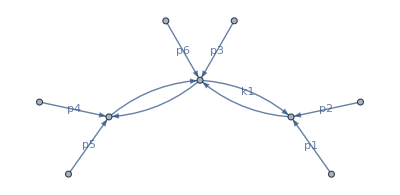

```mathematica
plotDiagram[hxb[1,0,1,0,0,1,0,1,0,0,0,0,0]]
```